# BoxPlot

```mathematica
importPath1=FileNameJoin[{$HomeDirectory,"Desktop","grafikdaten.xlsx"}];
data=Import[importPath1][[1]];
labels=data[[1]];
data=data[[2;;]];
```

```mathematica
dataTrans=Partition[Transpose[data],2]
```

{{{8.,31.,11.,9.,26.,14.,18.},{19.,11.,16.,9.,12.,25.,14.}},{{8.,8.,24.,10.,10.,16.,10.},{8.,8.,15.,25.,10.,9.,15.}},{{41.,60.,40.,51.,50.,30.,74.},{30.,37.,31.,41.,33.,80.,53.}},{{34.,22.,29.,25.,29.,31.,37.},{25.,20.,23.,45.,24.,29.,40.}}}

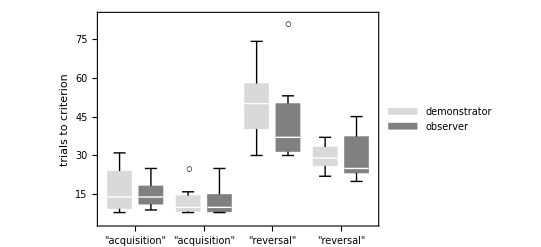

```mathematica
exportChart=BoxWhiskerChart[dataTrans,{"Outliers",
{"MedianMarker",1,Directive[Thick,White]},
{"Outliers","◦",Directive[FontSize->18,Black]},
{"FarOutliers","◦",Directive[Black]},
{"Whiskers",Thin},
{"Fences",Thin}},
BaseStyle->{FontFamily->"Arial",FontSize->14},
ChartLabels->{{"acquisition","acquisition","reversal","reversal"},
{Style["tool discrimination",FontSize->10],Style["association",FontSize->10]}},
ChartLegends->Placed[{"demonstrator","observer"},{{Right,Top}},Style[#,FontFamily->"Arial",FontSize->14]&],
Frame->{True,True,None,None},
ChartBaseStyle->{EdgeForm[Thickness[.001]]},
ChartStyle->{LightGray,Gray},
BarSpacing->Small,
ChartElementFunction->"BoxWhisker",
Method->{"BoxRange"->(Quantile[#,Range[0,1,1/4],{{1/2, 0}, {0, 1}}]&)},
(*PlotLabel->"Whatever",*)
FrameLabel->{"","trials to criterion"},
Joined->False,
PlotRange->All,
ImageSize->Scaled[1]]
```

```mathematica
Export["theBigBoxes.eps",exportChart]
```

theBigBoxes.eps

## Diffenrent common quantile ranges:

```mathematica
ChartElementFunction["BoxWhiskerCharts"]
```

ChartElementFunction[BoxWhiskerCharts]

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 0}, {1, 0}}]
```

{0.,0.2,0.5,0.8,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 0}, {0, 1}}]
```

{0.,0.175,0.45,0.725,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/2, 0}, {0, 0}}]
```

{0.,0.2,0.5,0.7,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/2, 0}, {0, 1}}]
```

{0.,0.225,0.5,0.775,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 1}, {0, 1}}]
```

{0.,0.2,0.5,0.8,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1, -1}, {0, 1}}]
```

{0.,0.25,0.5,0.75,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/3, 1/3}, {0, 1}}]
```

{0.,0.216667,0.5,0.783333,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{3/8, 1/4}, {0, 1}}]
```

{0.,0.21875,0.5,0.78125,1.}